```mathematica
$HistoryLength=0;
(* Unifying all the scripts *)
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
Get["G:\\LAT\\sd_metropolis\\apps\\pcm_wc_mspace\\pcm_wc_mspace_exact.m"];
Get["G:\\LAT\\sd_metropolis\\apps\\pcm_wc_mspace\\pcm_wc_mspace_analysis.m"];
(* Simulation parameters *)GetConvergenceSummary[LT_,LS_,λ_,mmax_,datadir_,labels_,output_]:=Module[{Suffix,ScalarFileName,ScalarData,np,label,ExactData,GxExtrapolation,LinkExtrapolation,MeanNFactor,CorrelatorsPlot,MidPointExtrapolation,iλpos,mcdata,ilt,ilts},
Suffix="d2_t"<>ToString[LT]<>"_s"<>ToString[LS]<>"_l"<>fsndig[λ,4];
ScalarData={};
Do[
ScalarFileName=datadir<>"\\scalars_"<>Suffix<>label<>".dat";
If[FileExistsQ[ScalarFileName],
If[output,Print["Importing the scalar data from ",ScalarFileName]];
(* Importing the scalar data, obtaining the mean values and the correlation matrices *)
ScalarData=Join[ScalarData,Import[ScalarFileName,"Table"]];
];,
{label,labels}];
np=Quotient[Length[ScalarData],mmax+1];
ExactData=ExactCorrelators[LT,LS,λ];
GxExtrapolation=NoisyScalarDataExtrapolation[ScalarData,2,(mmax+1),ExactData[[1]],{1,√x,x},x,2];
LinkExtrapolation=NoisyScalarDataExtrapolation[ScalarData,4,(mmax+1),ExactData[[3]],{1,√x,x},x,2];
MeanNFactor=0.5(GxExtrapolation[[2]]+LinkExtrapolation[[2]]);
{CorrelatorsPlot,MidPointExtrapolation}=ImportCorrelators[Table[datadir<>"\\Gxy_"<>Suffix<>label,{label,labels}],LS,mmax+1,MeanNFactor,ExactData[[5]],{1,√x,x},x];
If[output,
PrintScalarDataExtrapolation[GxExtrapolation,"Gx"];
PrintScalarDataExtrapolation[LinkExtrapolation,"Link"];
Print[Show[GraphicsGrid[{{GxExtrapolation[[3]],LinkExtrapolation[[3]],MidPointExtrapolation[[3]]}}],ImageSize->1000]];
Print["Mean NFactor is ",MeanNFactor," with ",np," data points"];
If[Abs[λ-3.0120]<0.0001,
ilts=Position[MCLTS,LT][[1]];
If[Length[ilts]>0,ilt=ilts[[1]];
Print["ilt = ",ilt];
Print[Show[CorrelatorsPlot,MCCorrelatorPlots[[ilt]],ImageSize->600]];,
Print[Show[CorrelatorsPlot,ImageSize->600]];
];,
Print[Show[CorrelatorsPlot,ImageSize->600]];
];
];
{LinkExtrapolation[[1,1]],LinkExtrapolation[[1,2]],MidPointExtrapolation[[1,1]],MidPointExtrapolation[[1,2]],MeanNFactor,np,MidPointExtrapolation[[3]]}
];
ScanDataset[paramset_,datadir_,labels_,xcol_,ycols_]:=Module[{params,csum,ycol},
Transpose[Table[
csum=GetConvergenceSummary[params[[1]], params[[2]],params[[3]],params[[4]],datadir,labels,True];
Table[csum[[ycol]],{ycol,ycols}]
,{params,paramset}]]
];
```

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t4_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t4_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t4_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t4_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t4_s108_l3.0120_itep2.dat

Gx = 0.124654 +/- 0.0147612, NFactor = 15060.

Link = 0.510135 +/- 0.0130432, NFactor = 15058.9

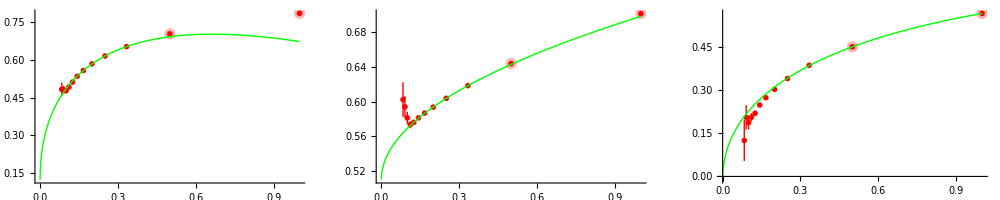

Mean NFactor is 15059.4 with 8249 data points

Part::partw: Part 1 of {} does not exist.

ilt = {}

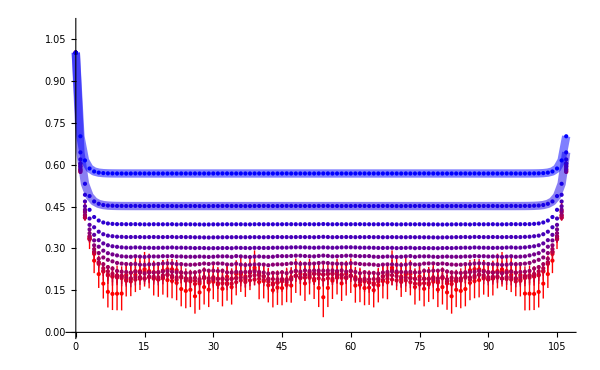

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t8_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t8_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t8_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t8_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t8_s108_l3.0120_itep2.dat

Gx = 0.337617 +/- 0.0102776, NFactor = 10131.8

Link = 0.545309 +/- 0.0101979, NFactor = 10129.1

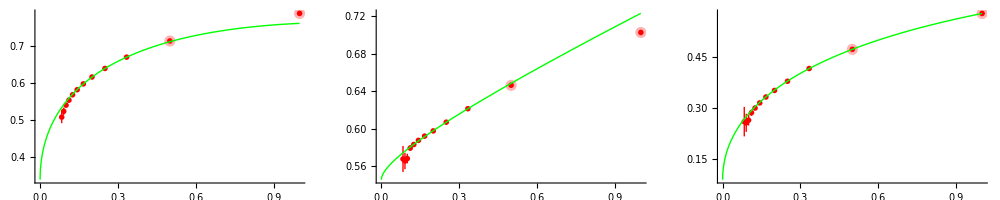

Mean NFactor is 10130.4 with 7778 data points

Part::partw: Part 1 of {} does not exist.

ilt = {}

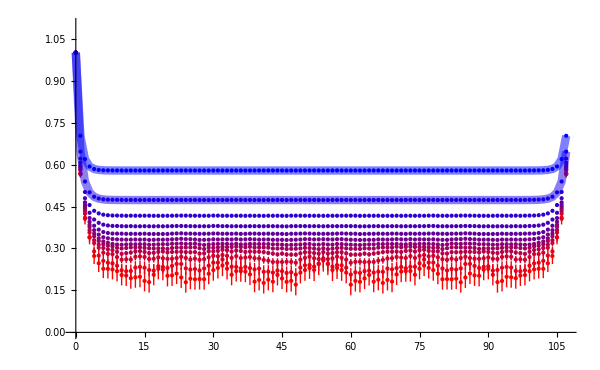

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t12_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t12_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t12_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t12_s108_l3.0120_itep2.dat

Gx = 0.349539 +/- 0.010713, NFactor = 9901.54

Link = 0.535713 +/- 0.0109703, NFactor = 9895.5

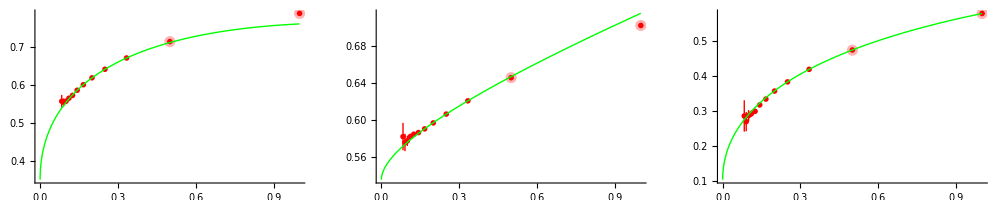

Mean NFactor is 9898.52 with 6528 data points

ilt = 1

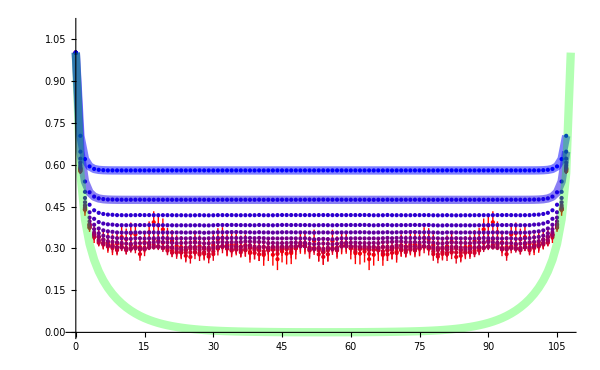

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t16_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t16_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t16_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t16_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t16_s108_l3.0120_itep2.dat

Gx = 0.3678 +/- 0.0100281, NFactor = 9895.21

Link = 0.535194 +/- 0.0102588, NFactor = 9900.99

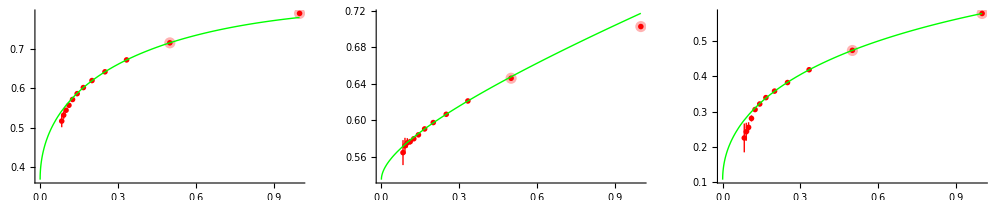

Mean NFactor is 9898.1 with 7537 data points

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

ilt = {}

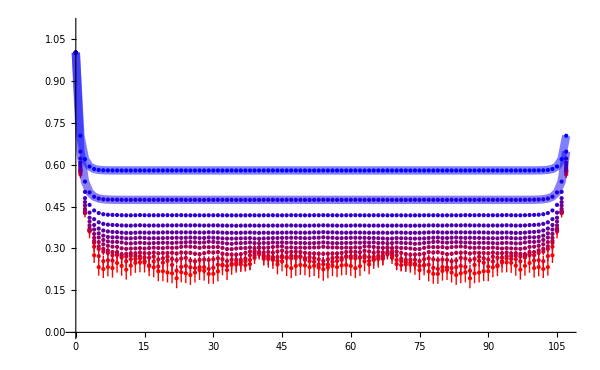

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t20_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t20_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t20_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t20_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t20_s108_l3.0120_itep2.dat

Gx = 0.373216 +/- 0.0096272, NFactor = 9883.63

Link = 0.540873 +/- 0.0098967, NFactor = 9887.15

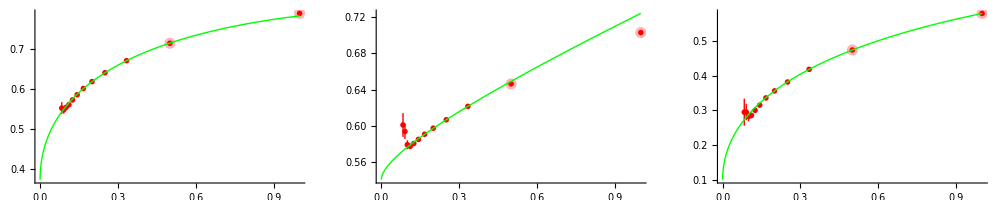

Mean NFactor is 9885.39 with 8400 data points

ilt = {}

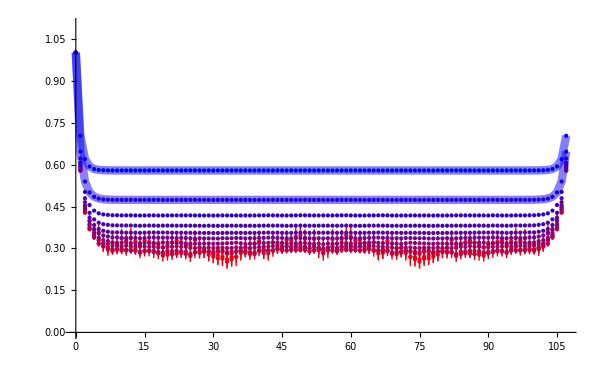

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t24_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t24_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t24_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t24_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t24_s108_l3.0120_itep2.dat

Gx = 0.352804 +/- 0.00943493, NFactor = 9892.44

Link = 0.542627 +/- 0.00963251, NFactor = 9895.14

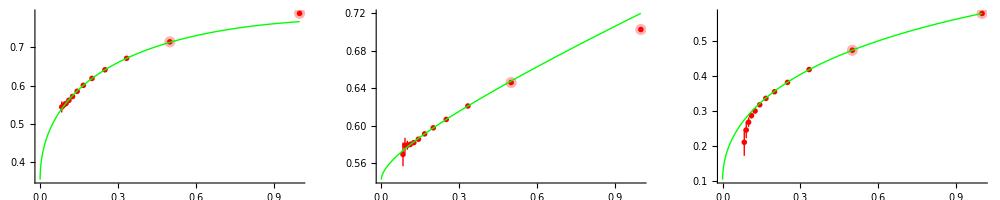

Mean NFactor is 9893.79 with 8661 data points

ilt = 3

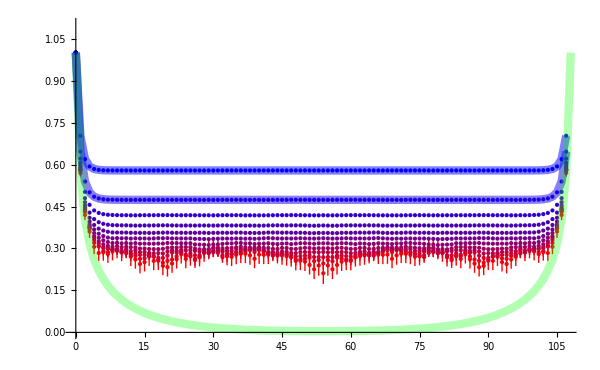

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t28_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t28_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t28_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t28_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t28_s108_l3.0120_itep2.dat

Gx = 0.362737 +/- 0.00948948, NFactor = 9874.2

Link = 0.548348 +/- 0.0098311, NFactor = 9876.39

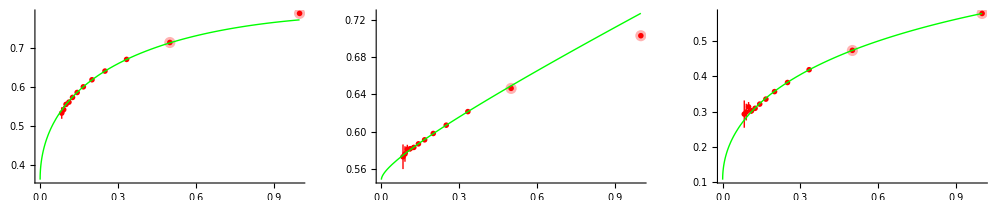

Mean NFactor is 9875.29 with 8364 data points

ilt = {}

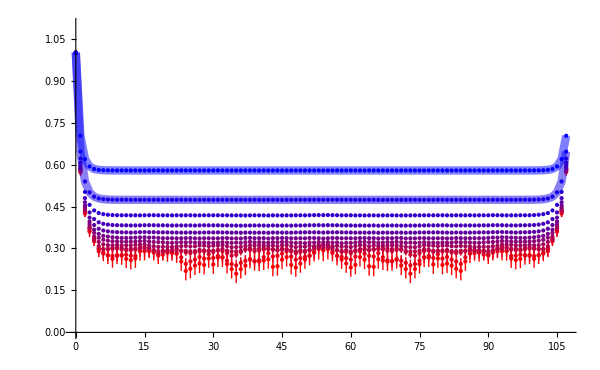

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t32_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t32_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t32_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t32_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t32_s108_l3.0120_itep2.dat

Gx = 0.348885 +/- 0.00956176, NFactor = 9878.89

Link = 0.540537 +/- 0.00977542, NFactor = 9881.08

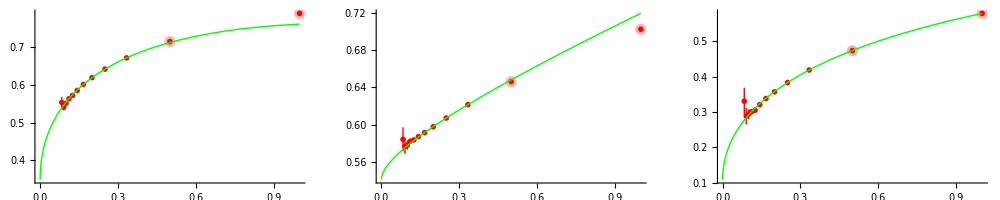

Mean NFactor is 9879.99 with 8578 data points

ilt = {}

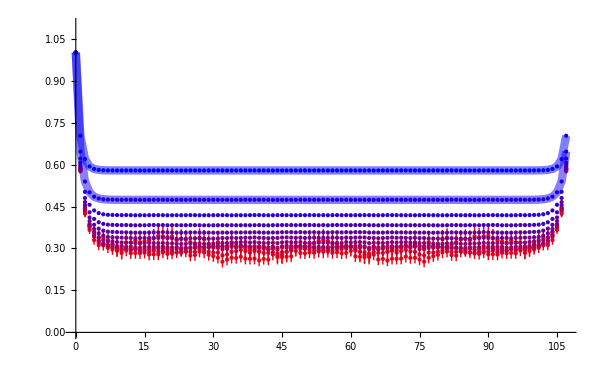

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t34_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t34_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t34_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t34_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t34_s108_l3.0120_itep2.dat

Gx = 0.345482 +/- 0.00935154, NFactor = 9890.87

Link = 0.522757 +/- 0.00966927, NFactor = 9890.99

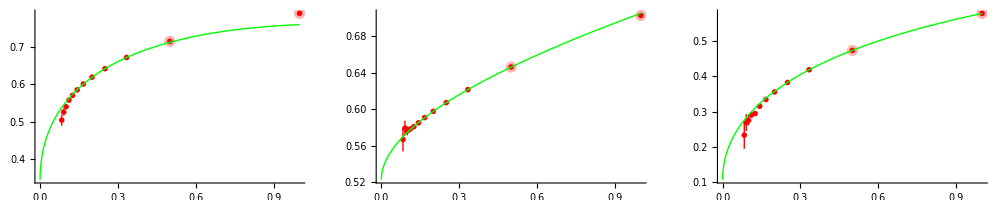

Mean NFactor is 9890.93 with 8433 data points

ilt = {}

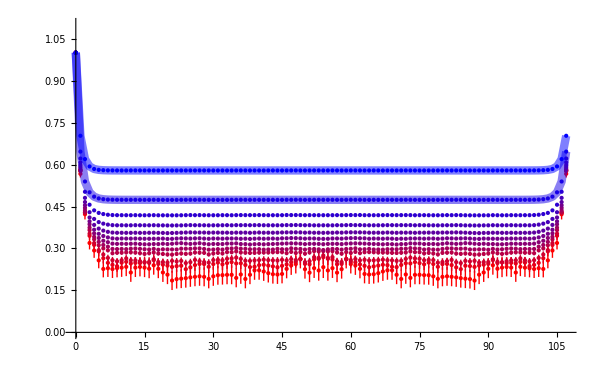

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t36_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t36_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t36_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t36_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t36_s108_l3.0120_itep2.dat

Gx = 0.353408 +/- 0.00960962, NFactor = 9896.1

Link = 0.532097 +/- 0.00978144, NFactor = 9896.92

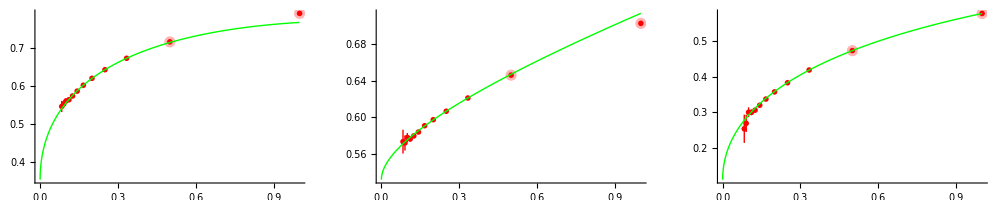

Mean NFactor is 9896.51 with 8396 data points

ilt = 4

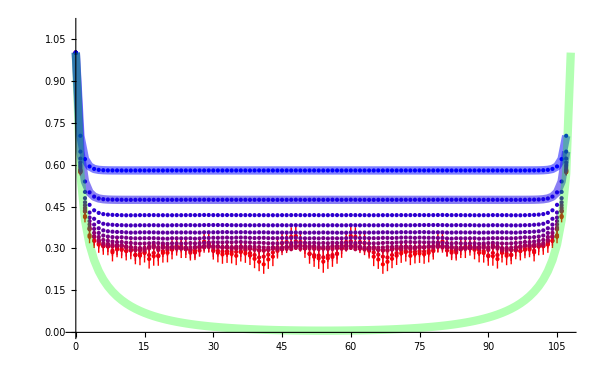

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t38_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t38_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t38_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t38_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t38_s108_l3.0120_itep2.dat

Gx = 0.367443 +/- 0.00975424, NFactor = 9902.8

Link = 0.538489 +/- 0.0099492, NFactor = 9903.45

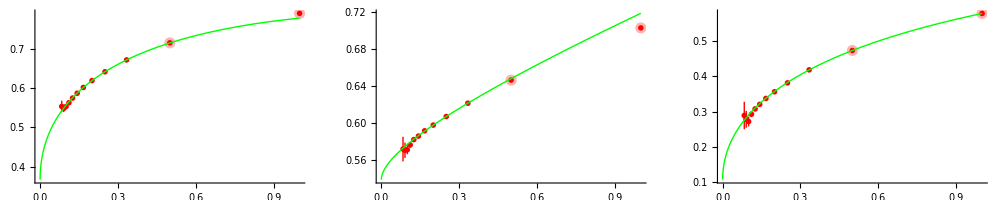

Mean NFactor is 9903.12 with 8331 data points

ilt = {}

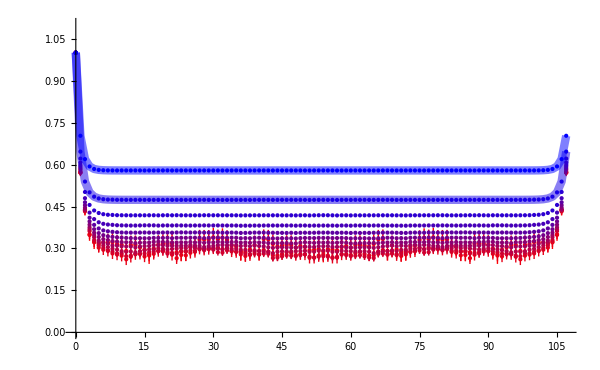

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t40_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t40_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t40_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t40_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t40_s108_l3.0120_itep2.dat

Gx = 0.350993 +/- 0.00967816, NFactor = 9883.16

Link = 0.53675 +/- 0.00987915, NFactor = 9884.49

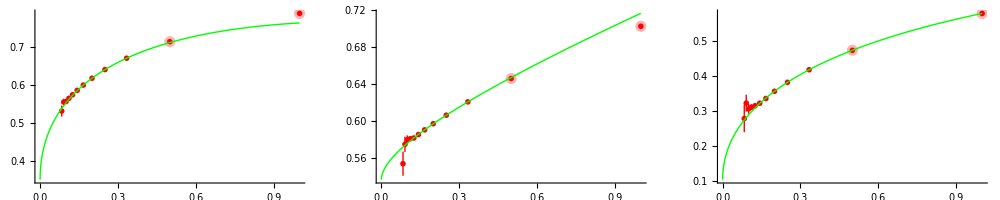

Mean NFactor is 9883.82 with 8388 data points

ilt = {}

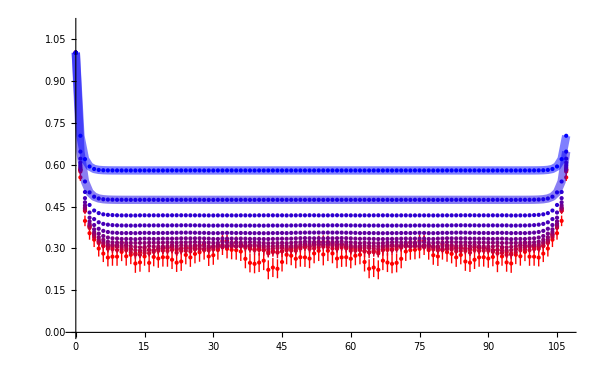

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t42_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t42_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t42_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t42_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t42_s108_l3.0120_itep2.dat

Gx = 0.353728 +/- 0.00955398, NFactor = 9899.32

Link = 0.542223 +/- 0.00981636, NFactor = 9898.57

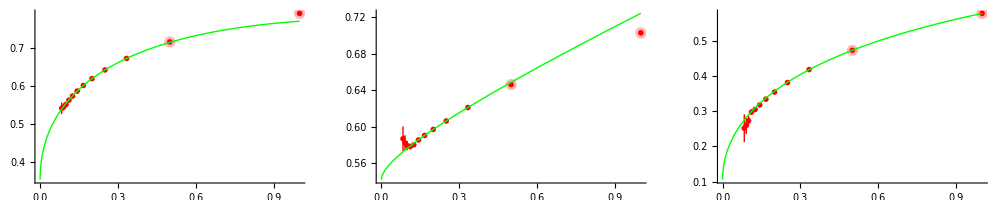

Mean NFactor is 9898.94 with 8192 data points

ilt = {}

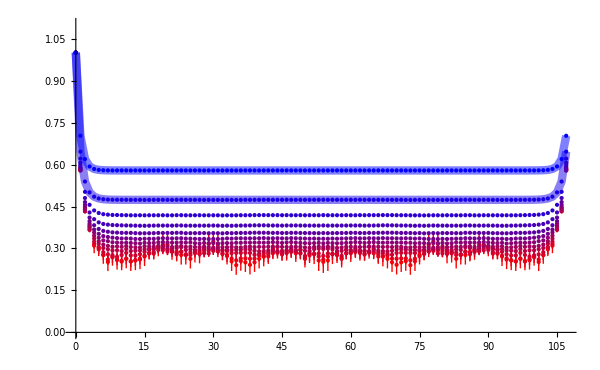

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t48_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t48_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t48_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t48_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t48_s108_l3.0120_itep2.dat

Gx = 0.341008 +/- 0.00969246, NFactor = 9890.23

Link = 0.532296 +/- 0.00994753, NFactor = 9890.27

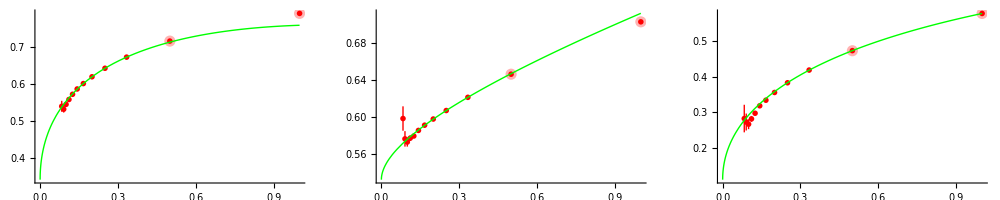

Mean NFactor is 9890.25 with 8313 data points

ilt = 5

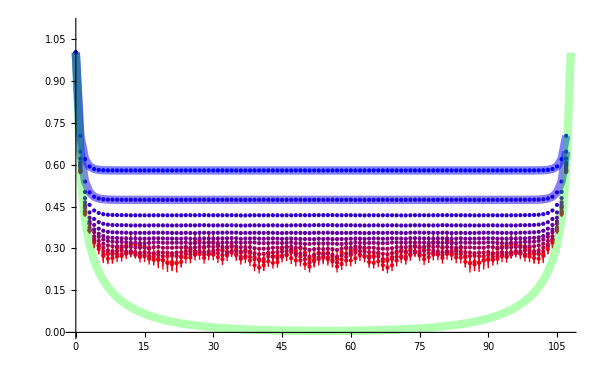

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t54_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t54_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t54_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t54_s108_l3.0120_itep1.dat

Gx = 0.364349 +/- 0.0102098, NFactor = 9890.13

Link = 0.531417 +/- 0.010534, NFactor = 9889.84

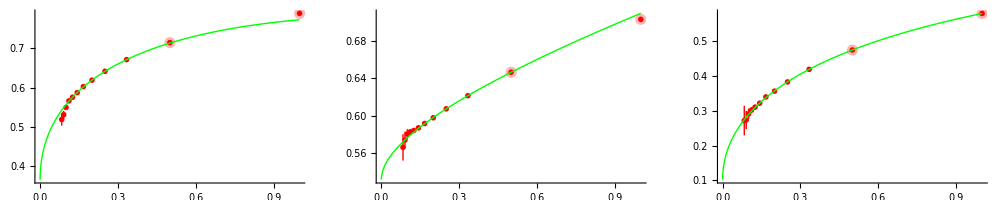

Mean NFactor is 9889.99 with 7327 data points

ilt = 6

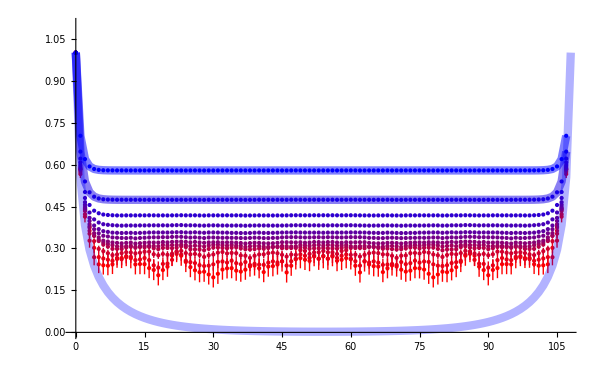

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t60_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t60_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t60_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t60_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t60_s108_l3.0120_itep2.dat

Gx = 0.364507 +/- 0.00950334, NFactor = 9882.89

Link = 0.533439 +/- 0.00970152, NFactor = 9883.54

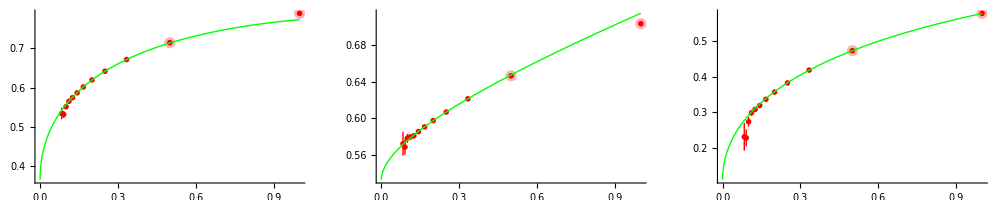

Mean NFactor is 9883.22 with 8439 data points

ilt = 7

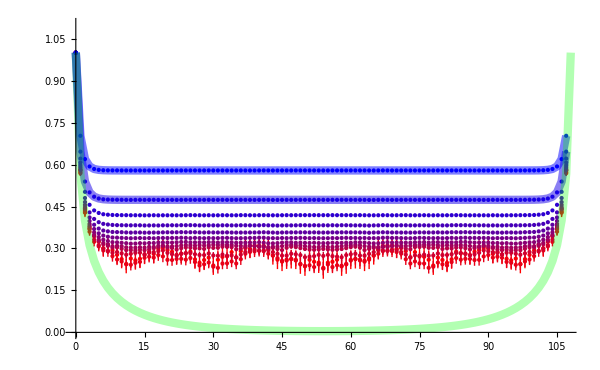

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t66_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t66_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t66_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t66_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t66_s108_l3.0120_itep2.dat

Gx = 0.363161 +/- 0.00972707, NFactor = 9885.36

Link = 0.545481 +/- 0.00990659, NFactor = 9883.87

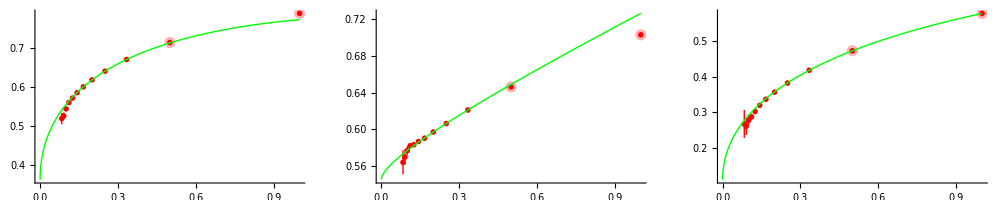

Mean NFactor is 9884.61 with 8253 data points

ilt = {}

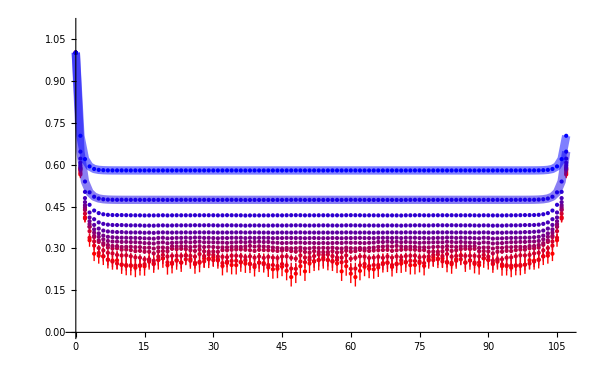

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t72_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t72_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t72_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t72_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t72_s108_l3.0120_itep2.dat

Gx = 0.367575 +/- 0.00969069, NFactor = 9884.48

Link = 0.533187 +/- 0.00995149, NFactor = 9888.65

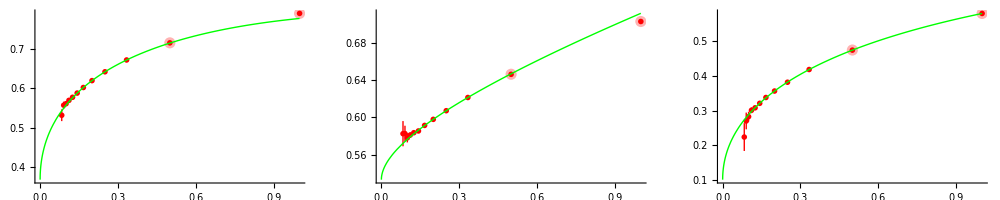

Mean NFactor is 9886.57 with 8151 data points

ilt = 8

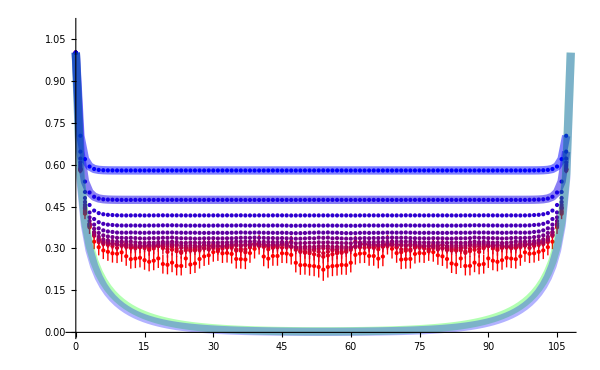

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t90_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t90_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t90_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t90_s108_l3.0120_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t90_s108_l3.0120_itep2.dat

Gx = 0.338542 +/- 0.00980266, NFactor = 9894.84

Link = 0.533942 +/- 0.0100313, NFactor = 9894.06

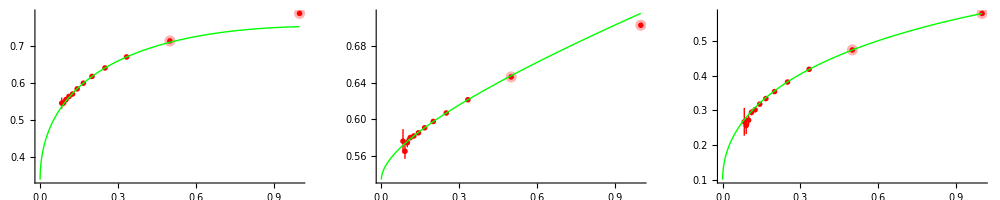

Mean NFactor is 9894.45 with 8132 data points

ilt = 10

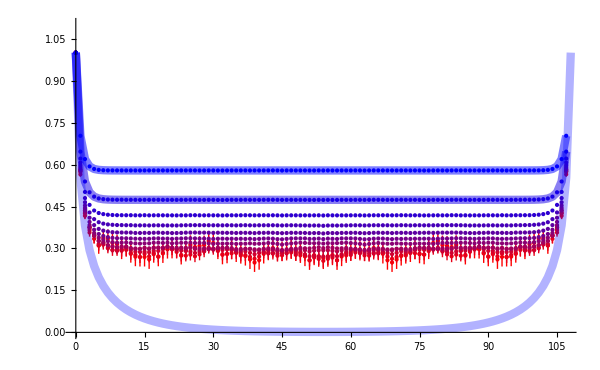

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.0120_idc.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.0120_idc1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.0120_itep1.dat

Gx = 0.344698 +/- 0.0105016, NFactor = 9901.81

Link = 0.53287 +/- 0.0104775, NFactor = 9903.49

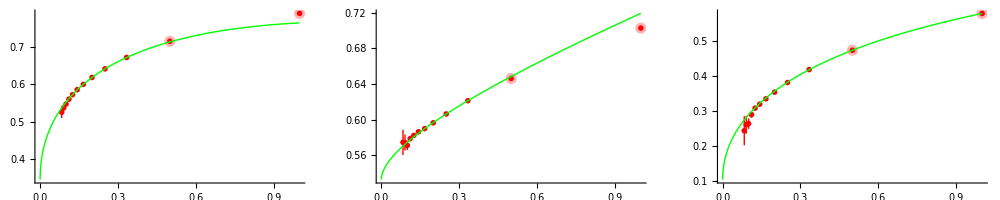

Mean NFactor is 9902.65 with 7294 data points

ilt = 12

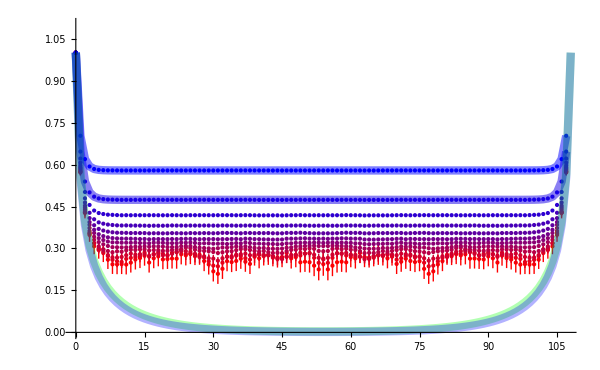

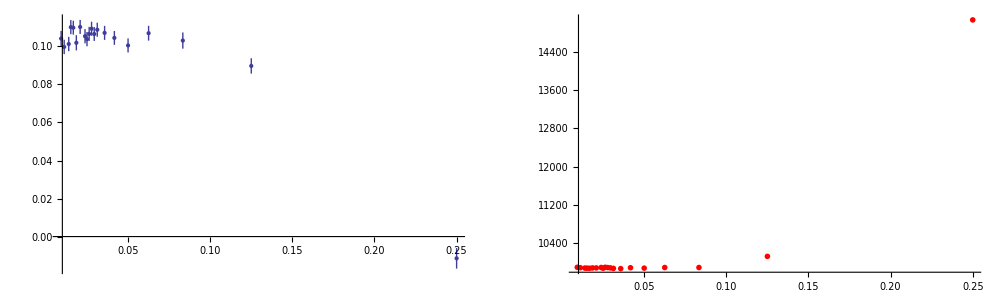

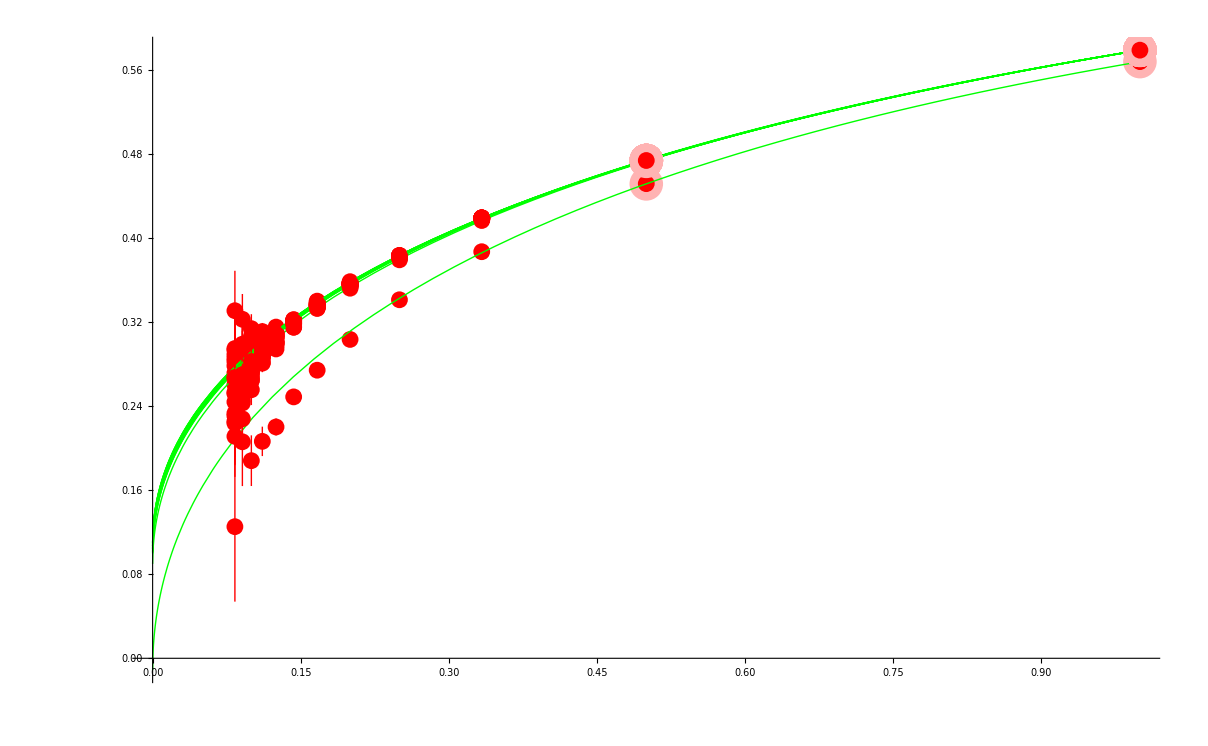

###################################################################################################################

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l5.0000.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l5.0000_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l5.0000_itep2.dat

Gx = -0.225455 +/- 0.0584128, NFactor = 63819.2

Link = -0.055619 +/- 0.0827801, NFactor = 63875.2

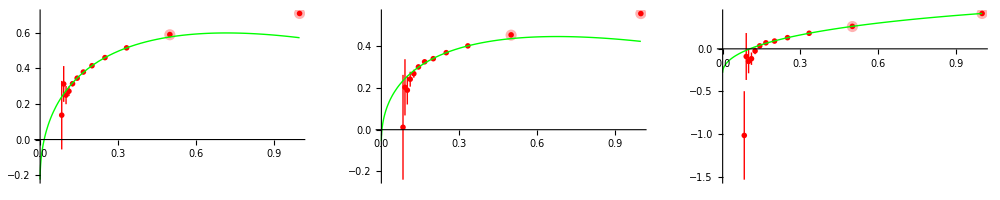

Mean NFactor is 63847.2 with 11290 data points

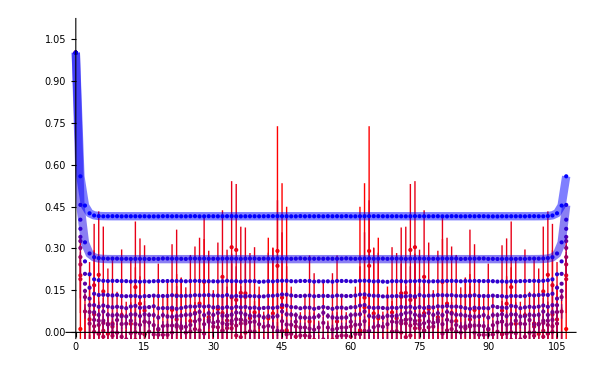

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l4.0000.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l4.0000_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l4.0000_itep2.dat

Gx = 0.0756255 +/- 0.0274466, NFactor = 27876.9

Link = 0.258825 +/- 0.0341979, NFactor = 27904.6

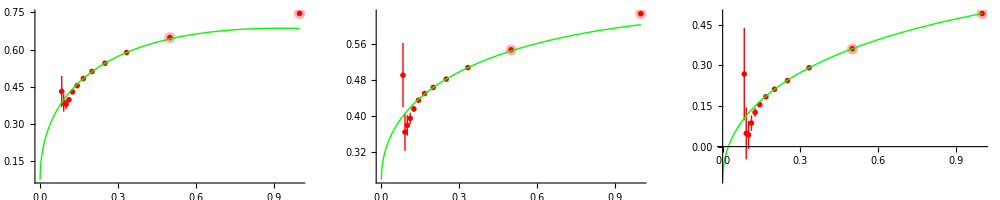

Mean NFactor is 27890.7 with 8909 data points

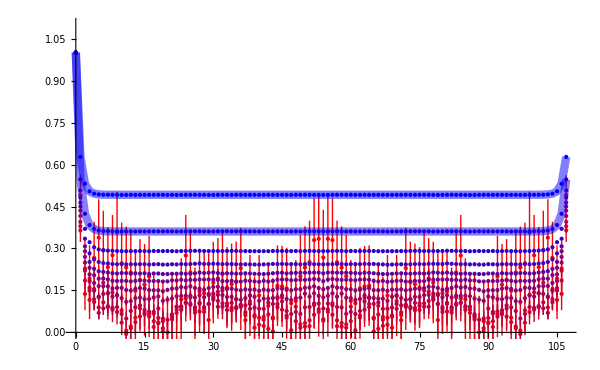

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.5700.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.5700_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.5700_itep2.dat

Gx = 0.217487 +/- 0.0188493, NFactor = 18275.8

Link = 0.39232 +/- 0.0219946, NFactor = 18289.

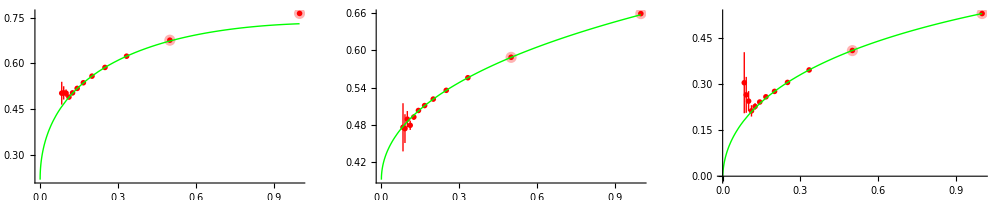

Mean NFactor is 18282.4 with 7571 data points

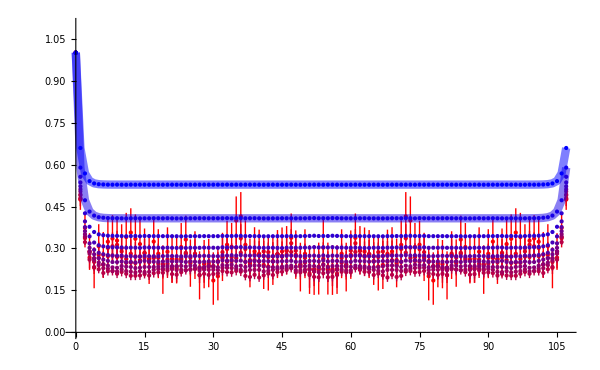

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.4500.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.4500_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.4500_itep2.dat

Gx = 0.215196 +/- 0.0170118, NFactor = 16091.9

Link = 0.439999 +/- 0.0189481, NFactor = 16091.3

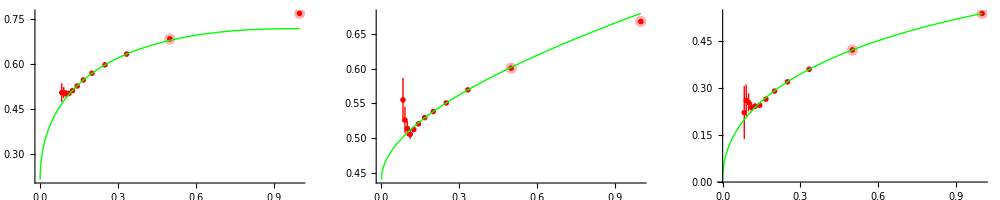

Mean NFactor is 16091.6 with 7333 data points

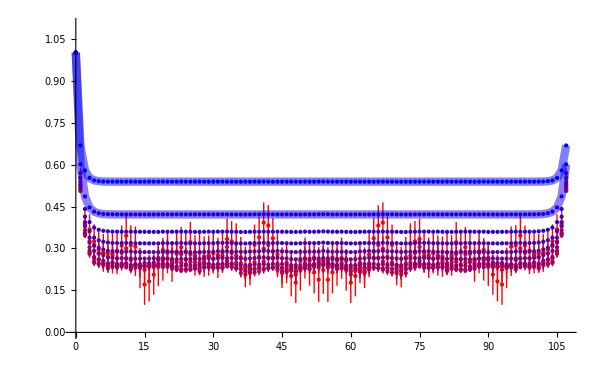

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.3300.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.3300_itep2.dat

Gx = 0.250255 +/- 0.017234, NFactor = 14176.7

Link = 0.455379 +/- 0.0189953, NFactor = 14177.2

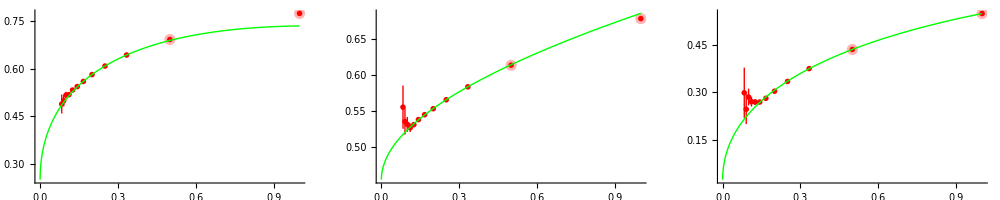

Mean NFactor is 14177. with 5728 data points

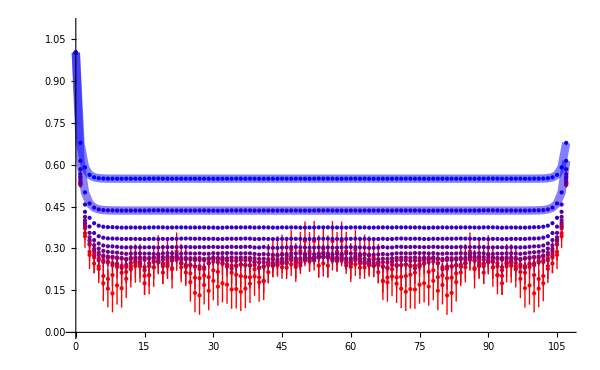

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.2300.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.2300_itep1.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.2300_itep2.dat

Gx = 0.286166 +/- 0.0140921, NFactor = 12670.8

Link = 0.46425 +/- 0.0149829, NFactor = 12675.2

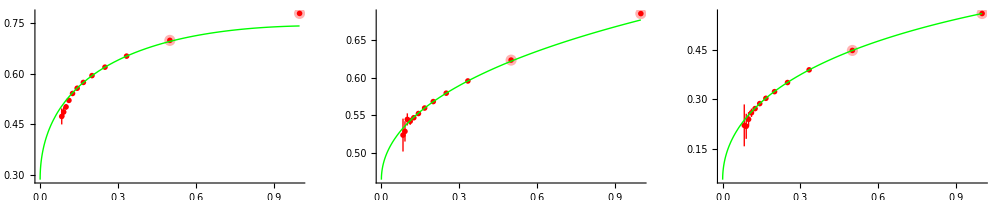

Mean NFactor is 12673. with 6579 data points

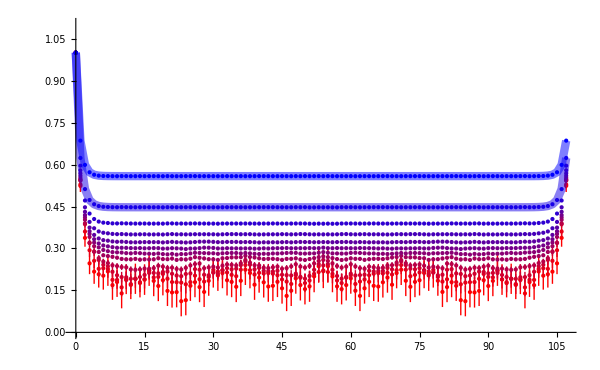

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.0120.dat

Importing the scalar data from C:\DATA\pcm_wc_mspace_raw_data\\scalars_d2_t108_s108_l3.0120_itep1.dat

Gx = 0.354174 +/- 0.012849, NFactor = 9900.91

Link = 0.538489 +/- 0.0128638, NFactor = 9904.56

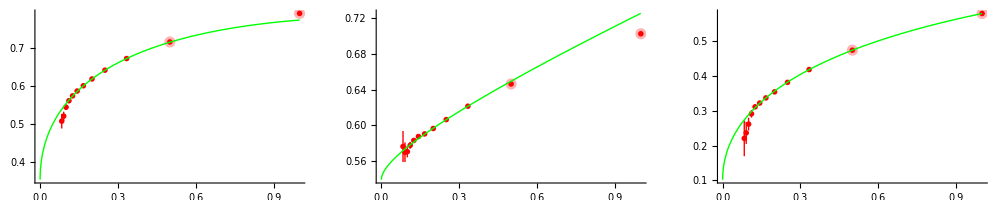

Mean NFactor is 9902.73 with 4887 data points

ilt = 12

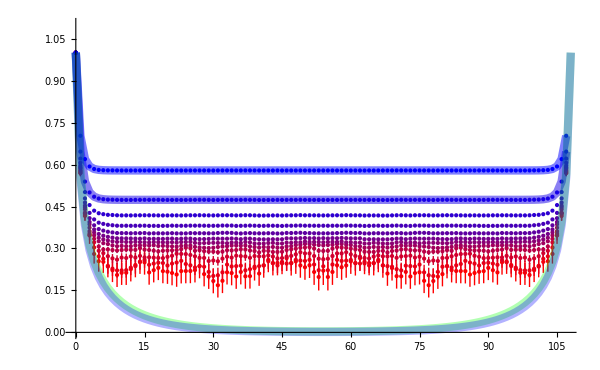

(-0.055619 | 0.258825 | 0.39232 | 0.439999 | 0.455379 | 0.46425 | 0.538489
0.0827801 | 0.0341979 | 0.0219946 | 0.0189481 | 0.0189953 | 0.0149829 | 0.0128638
-0.279436 | -0.122276 | -0.0113849 | 0.00742222 | 0.0233575 | 0.0580754 | 0.102246
0.0174356 | 0.00936671 | 0.00678071 | 0.00606544 | 0.00623371 | 0.00524928 | 0.00492937
63847.2 | 27890.7 | 18282.4 | 16091.6 | 14177. | 12673. | 9902.73)

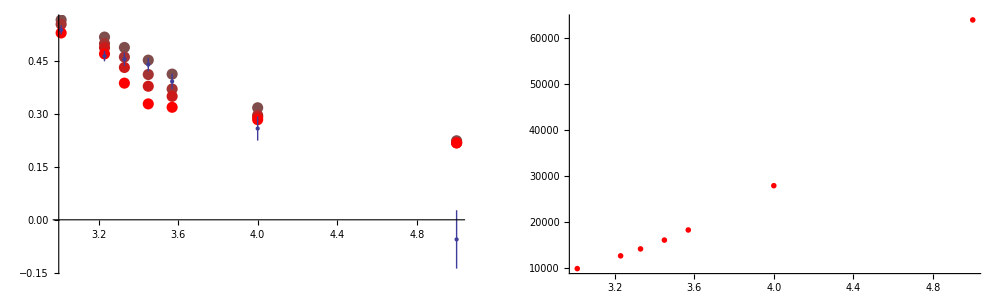

```mathematica
(* List of remote hosts *)
RemoteHosts={"di72kov@lxlogin5.lrz.de:/home/hpc/b3101/di72kov/", "bup58975@pcph00131.uni-regensburg.de:/lurch/home/bup58975/",
"buividovich@rrcmpi-a.itep.ru:/home/clusters/01/buividovich/"};
DataDirWin="C:\\DATA\\pcm_wc_mspace_raw_data\\";
DataDirLin="/c/DATA/pcm_wc_mspace_raw_data/";
(* Defining the finite T dataset *)
LTs={4, 8, 12, 16, 20,24,28,32,34,36,38,40,42,48,54,60,66,72,90,108};
TemperatureParameterSet=Table[{LT,108,3.0120,11},{LT,LTs}];
(* Defining the coupling dataset *)
λs={5.0,4.0,3.57,3.45,3.33,3.23,3.0120};
CouplingParameterSet=Table[{108,108,λ,11},{λ,λs}];
(* First updating the data *)
Do[
CMD="ssh-pageant rsync -v -z "<>RemoteHost<>"/sd_metropolis/data/pcm_wc_mspace/*.dat "<>DataDirLin;
Run[CMD];,
{RemoteHost,RemoteHosts}];
TemperatureRes=ScanDataset[TemperatureParameterSet,DataDirWin,{"","_idc","_idc1","_itep1","_itep2"},1,{1,2,3,4,5,7}];
(*Print[MatrixForm[TemperatureRes]];*)
GrMidPoint=PlotWithErrors[1/LTs,TemperatureRes[[3]],TemperatureRes[[4]],PlotRange->All];
GrNFactor=ListPlot[Transpose[{1/LTs,TemperatureRes[[5]]}],PlotRange->All,PlotStyle->{Red,PointSize[0.01]}];
Show[GraphicsGrid[{{GrMidPoint,GrNFactor}}],ImageSize->1000]
Show[TemperatureRes[[6]]]
Print["###################################################################################################################"];
CouplingRes=ScanDataset[CouplingParameterSet,DataDirWin,{"","_itep1","_itep2"},1,{1,2,3,4,5}];
Print[MatrixForm[CouplingRes]];
GrLink1=PlotWithErrors[λs,CouplingRes[[1]],CouplingRes[[2]]];
GrLink2=ListPlot[{VicariRossiN6Data,VicariRossiN9Data,VicariRossiN15Data,VicariRossiExtrapolatedData},PlotRange->All,PlotStyle->{{RGBColor[0.5,0.3,0.3],PointSize[0.02]},{RGBColor[0.65,0.2,0.2],PointSize[0.02]},{RGBColor[0.80,0.1,0.1],PointSize[0.02]},{RGBColor[1.0,0.0,0.0],PointSize[0.02]}}];
GrLink=Show[GrLink2,GrLink1];
GrNFactor=ListPlot[Transpose[{λs,CouplingRes[[5]]}],PlotRange->All,PlotStyle->{Red,PointSize[0.01]}];
Show[GraphicsGrid[{{GrLink,GrNFactor}}],ImageSize->1000]
```